```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 229 Kb

{Utilities`CleanSlate`,Parallel`Debug`Perfmon`,Parallel`Debug`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,System`,Global`}

```mathematica
Clear[za]
za = z[t] - 1/2 a ϕ[t] + 1/2 b θ[t]
```

z[t]+1/2 b θ[t]-1/2 a ϕ[t]

```mathematica
Clear[zb]
zb =  z[t] - 1/2 a ϕ[t] - 1/2 b θ[t]
```

z[t]-1/2 b θ[t]-1/2 a ϕ[t]

```mathematica
Clear[zc]
zc =  z[t] + 1/2 a ϕ[t] - 1/2 b θ[t]
```

z[t]-1/2 b θ[t]+1/2 a ϕ[t]

```mathematica
Clear[zd]
zd =  z[t] + 1/2 a ϕ[t] + 1/2 b θ[t]
```

z[t]+1/2 b θ[t]+1/2 a ϕ[t]

```mathematica
Clear[r]
r = { za , zb, zc, zd }
```

{z[t]+1/2 b θ[t]-1/2 a ϕ[t],z[t]-1/2 b θ[t]-1/2 a ϕ[t],z[t]-1/2 b θ[t]+1/2 a ϕ[t],z[t]+1/2 b θ[t]+1/2 a ϕ[t]}

```mathematica
r . r
```

(z[t]-1/2 b θ[t]-1/2 a ϕ[t])^2+(z[t]+1/2 b θ[t]-1/2 a ϕ[t])^2+(z[t]-1/2 b θ[t]+1/2 a ϕ[t])^2+(z[t]+1/2 b θ[t]+1/2 a ϕ[t])^2

```mathematica
r . r  // Expand
```

4 z[t]^2+b^2 θ[t]^2+a^2 ϕ[t]^2

```mathematica
Clear[T] 
T = 1/2 M z'[t]^2 + 1/2(1/12 M a^2 ϕ'[t]^2 ) + 1/2(1/12 M b^2 θ'[t]^2 )
```

1/2 M z'[t]^2+1/24 b^2 M θ'[t]^2+1/24 a^2 M ϕ'[t]^2

```mathematica
Clear[V]
V = 1/2 k ( r . r ) + M g z[t] // Expand
```

g M z[t]+2 k z[t]^2+1/2 b^2 k θ[t]^2+1/2 a^2 k ϕ[t]^2

```mathematica
Clear[ℒ]
ℒ = T - V ;
ℒ // pdConv
```

-1/2 a^2 k (ϕ(t))^2+1/24 a^2 M ((∂ϕ(t))/(∂t))^2-1/2 b^2 k (θ(t))^2+1/24 b^2 M ((∂θ(t))/(∂t))^2-g M z(t)-2 k (z(t))^2+1/2 M ((∂z(t))/(∂t))^2

```mathematica
Clear[q]
q = { z[t] , ϕ[t] , θ[t] }
```

{z[t],ϕ[t],θ[t]}

```mathematica
D[ ℒ , D[q[[1]], t] ] - D[ ℒ , q[[1]] ] 
D[ ℒ , D[q[[2]], t] ] - D[ ℒ , q[[2]] ]
D[ ℒ , D[q[[3]], t] ] - D[ ℒ , q[[3]] ]
```

g M+4 k z[t]+M z'[t]

a^2 k ϕ[t]+1/12 a^2 M ϕ'[t]

b^2 k θ[t]+1/12 b^2 M θ'[t]

```mathematica
Table[ 
D[ ℒ , D[q[[i]], t] ] - D[ ℒ , q[[i]] ]== 0  , 
{ i, 1, 3 } ] // Simplify // TableForm
```

4 k z[t]+M (g+z'[t])==0
12 a k ϕ[t]+a M ϕ'[t]==0
12 b k θ[t]+b M θ'[t]==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

-4 k z[t]-M (g+z''[t])==0
-1/12 a^2 (12 k ϕ[t]+M ϕ''[t])==0
-1/12 b^2 (12 k θ[t]+M θ''[t])==0

```mathematica
Clear[parameters]
parameters = { 
a -> 4 , 
b -> 2 , 
M ->20 , 
g -> 9.8 ,
k-> 50
} ; 
parameters // TableForm
```

a→4
b→2
M→20
g→9.8
k→50

```mathematica
eqs /. parameters // Expand // TableForm
```

-196.-200 z[t]-20 z''[t]==0
-800 ϕ[t]-(80 ϕ''[t])/3==0
-200 θ[t]-(20 θ''[t])/3==0

```mathematica
Clear[ics]
ics = { 
z[0] == 0.1 , 
z'[0] == 0.1 ,
θ[0] == 0 ,
θ'[0] == -0.2 ,
ϕ[0] == 0 ,
ϕ'[0] == 0.05 
} ;
ics // TableForm
```

z[0]==0.1
z'[0]==0.1
θ[0]==0
θ'[0]==-0.2
ϕ[0]==0
ϕ'[0]==0.05

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 100 } ]]
```

{z[t]→InterpolatingFunction[…][t],ϕ[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

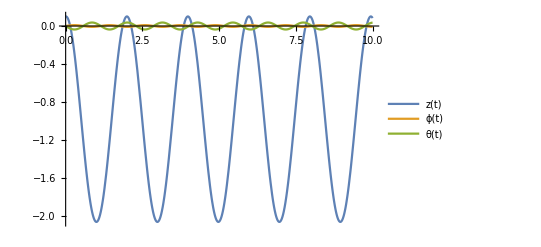

```mathematica
Plot[ Evaluate[ q /. solution[t] ]  , { t , 0, 10 } , PlotLegends -> q  ]
```

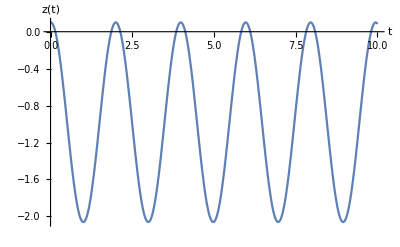

```mathematica
Plot[ q[[1]] /. solution [t], { t , 0, 10 }, AxesLabel-> { t , q[[1]] } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 1 , 20 , 0.5  } ]
```

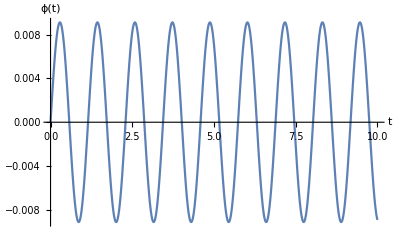

```mathematica
Plot[ q[[2]] /. solution [t], { t , 0, 10 }, AxesLabel-> { t , q[[2]] } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, tmax } , AxesLabel-> { q[[2]] , D[q[[2]], t] } ]  ,
{ tmax , 1 , 20 , 0.5  } ]
```

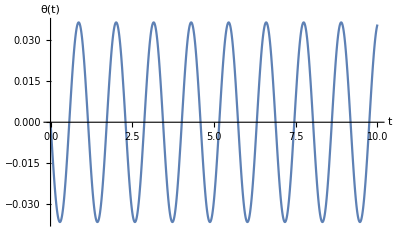

```mathematica
Plot[ q[[3]] /. solution[t] , { t , 0, 10 },  AxesLabel-> { t , q[[3]] } ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[3,2]] , solution'[t][[3,2]] } , { t , 0, tmax } , AxesLabel-> { q[[3]] , D[q[[3]], t] } ]  ,
{ tmax , 1 , 20 , 0.5  } ]
```